```mathematica
dataNitroC=Flatten[Import["/Users/rhariadi/Downloads/NitroC.001.csv"]];
dataHMDS=Join[Flatten[Import["/Users/rhariadi/Downloads/HMDS.001.csv"]],{110}];
```

```mathematica
(*dataSortNitroC=Sort[dataNitroC];
dataSortHMDS=Sort[dataHMDS];*)
```

```mathematica
(*dataCDFNitroC=Table[{dataSortNitroC⟦i⟧,i/Length[dataSortNitroC]},{i,1,Length[dataSortNitroC]}];
dataCDFHMDS=Table[{dataSortHMDS⟦i⟧,i/Length[dataSortHMDS]},{i,1,Length[dataSortHMDS]}];*)
```

```mathematica
(*ListLinePlot[{dataCDFHMDS,dataCDFNitroC},PlotRange->{{-10,110},{0,1.05}},Frame->True,Axes->False,FrameTicks->{{0,0.5,{1,"1.0"},None},{{0,25,50,75,100},None}},FrameLabel -> {{"CDF", None}, {"Height (nm)", None}},ImageSize->300,Filling->Axis]*)
```

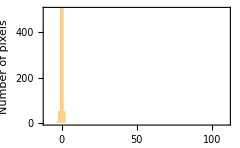

```mathematica
Histogram[dataHMDS,{-10,110,1.25},PlotRange->{0,500},Frame->{{True,False},{True,False}},Axes->False,FrameTicks->{{{0,200,400},None},{{0,25,50,75,100},None}},FrameLabel -> {{"Number of pixels", None}, {"Height (nm)", None}},ImageSize->240,FrameTicksStyle->Directive[FontFamily->"FlamaLight"],LabelStyle->Directive[FontFamily->"Flama"]]
```

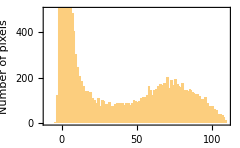

```mathematica
Histogram[dataNitroC,{-10,110,1.25},PlotRange->{0,500},Frame->{{True,False},{True,False}},Axes->False,FrameTicks->{{{0,200,400},None},{{0,25,50,75,100},None}},FrameLabel -> {{"Number of pixels", None}, {"Height (nm)", None}},ImageSize->240,FrameTicksStyle->Directive[FontFamily->"FlamaLight"],LabelStyle->Directive[FontFamily->"Flama"]]
```

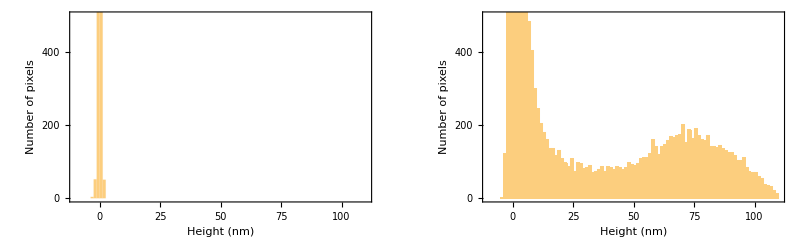

```mathematica
GraphicsGrid[{{-Graphics-,-Graphics-}}]
```

```mathematica
Export[$Failed,%143,"PDF"]
```

Export::chtype: First argument $Failed is not a valid file specification.

$Failed